Total time for generating DensityPlot and Plot3D: 737.915 minutes

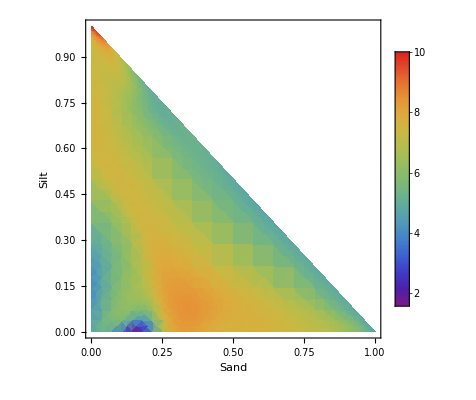

```mathematica
(*Written by Frederic Ouimet (November 2024)*)SetDirectory["C:\\Users\\fred1\\Dropbox\\Ouimet_Genest_projects\\Daayeb_Genest_Khardani_Klutchnikoff_Ouimet_2024\\simulations"];

(*Define the necessary functions*)
hatM[xx_,b_,s_,y_]:=Module[{n,d,u,v,kernelVec,designMat,W},n=Length[xx];
d=Length[xx[[1]]];
(*Calculate kernel vector*)u=s/b+ConstantArray[1,d];
v=(1-Total[s])/b+1;
kernelVec=Table[PDF[DirichletDistribution[Join[u,{v}]],xx[[i]]],{i,1,n}];
(*Local Linear Estimation*)designMat=Table[Join[{1},xx[[i]]-s],{i,1,n}];
W=DiagonalMatrix[kernelVec];
Return[First[LinearSolve[Transpose[designMat].W.designMat,Transpose[designMat].W.y]]];];

(*GEMAS dataset*)
(*Load CSV file and import data*)
data=Import["GEMAS.csv","CSV"];

(*Remove the header row and filter data*)
filteredData=Select[Rest[data],And@@(NumericQ[#]&&#=!=""&&#=!=Null&&Head[#]=!=Missing&/@#[[{15,16,17,25}]])&];

(*Extract relevant columns (15:sand_norm,16:silt_norm,17:clay_norm,25:pH_CaCl2)*)
vectors=filteredData[[All,{15,16,17,25}]];

(*Extract xx and y from the given vectors*)
xx=(vectors[[All,1;;2]])/100;
y=vectors[[All,4]];

(*Optimal b (b_opt_LOOCV from R)*)
b=0.0303333333333333;

hatMFunction[s1_,s2_]:=hatM[xx,b,{s1,s2},y];

(*Measure time for DensityPlot and Plot3D*)
time=AbsoluteTiming[
(*Create density plot*)densityPlot=DensityPlot[Evaluate[hatMFunction[s1,s2]],{s1,0,1},{s2,0,1},RegionFunction->Function[{s1,s2},s1+s2<=1],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LabelStyle->Directive[FontSize->18]],Right],ColorFunction->"Rainbow",Frame->True,FrameLabel->{Style["Sand",FontSize->22],Style["Silt",FontSize->22]},TicksStyle->Directive[FontSize->18],LabelStyle->Directive[FontSize->18]];][[1]]; (*Extract the time value*)


(*Convert time to minutes*)
timeInMinutes=time/60;

(*Display time difference*)
Print["Total time for generating DensityPlot and Plot3D: ",timeInMinutes," minutes"]

(*Display plots*)
Show[densityPlot]
```